```mathematica
ClearAll[sgm, rho, x, x0, s,ass];
sgm[x_, x0_, s_]:=1/(1+Exp[-((x-x0)/s)]);
rho[r_, rho0_, rhoInf_, r0_, s_, a_]:=rho0+(rhoInf-rho0)*sgm[r,r0,s]+a/r;

rhoP=FullSimplify[D[rho[r, rho0, rhoInf, r0, s, a],r]];
Print["rho' = ", rhoP];

ass={rho0>0, rhoInf>rho0, r0>0, s>0, a∈Reals};
solP=Solve[rhoP==0,Assumptions->ass];
Print["rhoP == 0: ", solP];
```

rho' = -a/r^2+((-rho0+rhoInf) Sech[(r-r0)/(2 s)]^2)/(4 s)

$Aborted

rhoP == 0: solP

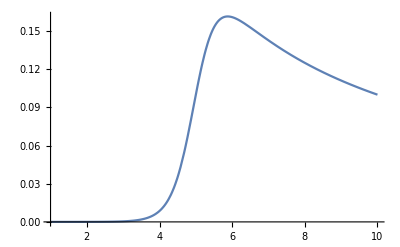

```mathematica
ClearAll[x0];
x0=5;
s=0.3;
x1=5;
xmin=1;
xmax=10;
a=1;
Plot[LogisticSigmoid[(x-x0)/s]*(a/x),{x, xmin, xmax},PlotRange->All]
```

1/(√(3 Gamma[4/3]))=0.610968

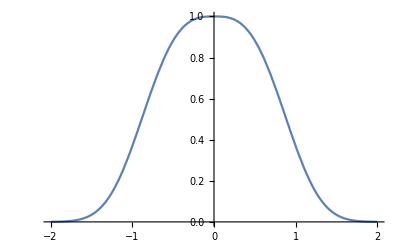

```mathematica
f[x_, s_]:=Exp[-(Abs[x]/s)^3];
ass={s>0};
sn=Sqrt[Integrate[f[x,s]*x^2,{x,-Infinity, Infinity},Assumptions->ass]/Integrate[f[x,s],{x,-Infinity, Infinity},Assumptions->ass]/s^2];
Print[sn, "=",N[sn]];
Plot[f[x,1],{x,-2,2}]
```